### Thermal states

```mathematica
LoadBosonicOperators[nmax=30]
βω = 1.0;
ρ = MatrixExp[-βω a†.a];
ρ = ρ/Tr[ρ]//mf;
```

Matrices loaded: 𝕀 (=1), a, 𝕏, ℙ, CoherentState[α], ThermalState[n0]

(0.632121 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.232544 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0855482 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0314714 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0115777 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00425919 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.00156687 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000576419 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000212053 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000780099 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000286982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000105575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.88388×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.4288×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.25626×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.93367×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.11358×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.61694×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.62718×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.54164×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.3029×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.79309×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.76328×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Tr[ρ]
```

1.

```mathematica
Tr[a.ρ]
```

0.

```mathematica
Tr[a†.a.ρ]
1/(ⅇ^βω-1)
```

0.581977

0.581977

```mathematica
Tr[a†.a.a†.a.ρ]
```

1.25937

### Coherent states

```mathematica
ψ = CoherentState[α=0.8+ 0.2 ⅈ]
```

{0.71177+0. ⅈ,0.569416+0.142354 ⅈ,0.301979+0.161055 ⅈ,0.120881+0.109258 ⅈ,0.0374266+0.0557912 ⅈ,0.00840003+0.023308 ⅈ,0.000840347+0.00829822 ⅈ,-0.000373189+0.00257267 ⅈ,-0.000287469+0.000701272 ⅈ,-0.00012341+0.000167841 ⅈ,-0.0000418357+0.0000346557 ⅈ,-0.000012181+5.83649×10^-6 ⅈ,-3.15005×10^-6+6.44611×10^-7 ⅈ,-7.34689×10^-7-3.17068×10^-8 ⅈ,-1.55388×10^-7-4.605×10^-8 ⅈ,-2.97189×10^-8-1.75363×10^-8 ⅈ,-5.06696×10^-9-4.9932×10^-9 ⅈ,-7.40929×10^-10-1.21461×10^-9 ⅈ,-8.24539×10^-11-2.63956×10^-10 ⅈ,-3.02184×10^-12-5.22278×10^-11 ⅈ,1.79513×10^-12-9.47793×10^-12 ⅈ,7.27035×10^-13-1.57626×10^-12 ⅈ,1.91215×10^-13-2.37846×10^-13 ⅈ,4.18158×10^-14-3.17013×10^-14 ⅈ,8.12269×10^-15-3.46968×10^-15 ⅈ,1.43842×10^-15-2.3024×10^-16 ⅈ,2.34708×10^-16+2.02963×10^-17 ⅈ,3.53545×10^-17+1.21587×10^-17 ⅈ,4.88554×10^-18+3.1745×10^-18 ⅈ,6.0788×10^-19+6.53037×10^-19 ⅈ}

```mathematica
ψ*.a.ψ
```

0.8+0.2 ⅈ

```mathematica
ψ*.a†.a.ψ//Chop
Abs[α]^2
```

0.68

0.68

```mathematica
a.ψ-α ψ//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
X1 = 1/2(a+a†);
X2 = ⅈ/2(a†-a);
ψ*.X1.ψ//Chop
ψ*.X2.ψ//Chop
```

0.8

0.2

```mathematica
ψ*.X1.X1.ψ - Abs[ψ*.X1.ψ]^2//Chop
```

0.25

### Poisson distribution for coherent states

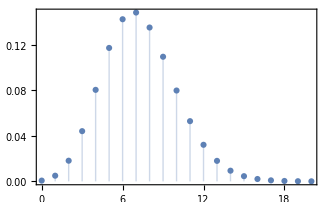

```mathematica
αα = 2.7;
ListPlot[Abs[CoherentState[αα]]^2,
PlotMarkers->Automatic,
Filling->Axis,
PlotRange->{{0,20},All},
DataRange->{0,nmax-1},
PlotRangePadding->Scaled[0.02]]
```

```mathematica
Abs[CoherentState[αα]]^2
Table[PDF[PoissonDistribution[Abs[αα]^2],n],{n,0,nmax-1}]
```

{0.000682328,0.00497417,0.0181309,0.044058,0.0802957,0.117071,0.142241,0.148134,0.134987,0.10934,0.0797087,0.0528251,0.0320912,0.0179958,0.00937066,0.00455414,0.00207498,0.000889801,0.000360369,0.000138268,0.0000503987,0.0000174955,5.79739×10^-6,1.83752×10^-6,5.58147×10^-7,1.62756×10^-7,4.56341×10^-8,1.23212×10^-8,3.20792×10^-9,8.06404×10^-10}

{0.000682328,0.00497417,0.0181309,0.044058,0.0802957,0.117071,0.142241,0.148134,0.134987,0.10934,0.0797087,0.0528251,0.0320912,0.0179958,0.00937066,0.00455414,0.00207498,0.000889801,0.000360369,0.000138268,0.0000503987,0.0000174955,5.79739×10^-6,1.83752×10^-6,5.58147×10^-7,1.62756×10^-7,4.56341×10^-8,1.23212×10^-8,3.20792×10^-9,8.06404×10^-10}

### Time evolution of coherent states

```mathematica
H = a†.a;
Δt = 0.1;
U = MatrixExp[-ⅈ Δt H];
ϕ = ψ;
Ψt = Table[ϕ=U.ϕ,{nsteps=100}];
Dimensions[Ψt]
```

{100,30}

```mathematica
X1t=Table[{n Δt, Ψt[[n]]*.X1.Ψt[[n]]},{n,nsteps}]//Chop
```

{{0.1,0.308485},{0.2,0.313887},{0.3,0.316153},{0.4,0.31526},{0.5,0.311217},{0.6,0.304065},{0.7,0.293874},{0.8,0.280748},{0.9,0.264816},{1.,0.246238},{1.1,0.2252},{1.2,0.201911},{1.3,0.176605},{1.4,0.149535},{1.5,0.120971},{1.6,0.0911975},{1.7,0.0605131},{1.8,0.0292241},{1.9,-0.00235686},{2.,-0.0339143},{2.1,-0.0651329},{2.2,-0.0957007},{2.3,-0.125312},{2.4,-0.153672},{2.5,-0.180496},{2.6,-0.205516},{2.7,-0.228484},{2.8,-0.249168},{2.9,-0.267363},{3.,-0.282886},{3.1,-0.295582},{3.2,-0.305326},{3.3,-0.312019},{3.4,-0.315594},{3.5,-0.316015},{3.6,-0.31328},{3.7,-0.307414},{3.8,-0.298476},{3.9,-0.286556},{4.,-0.271773},{4.1,-0.254275},{4.2,-0.234236},{4.3,-0.211856},{4.4,-0.18736},{4.5,-0.160992},{4.6,-0.133015},{4.7,-0.103709},{4.8,-0.0733668},{4.9,-0.0422916},{5.,-0.0107938},{5.1,0.0208119},{5.2,0.0522095},{5.3,0.0830856},{5.4,0.113131},{5.5,0.142047},{5.6,0.169543},{5.7,0.195345},{5.8,0.219196},{5.9,0.240856},{6.,0.26011},{6.1,0.276764},{6.2,0.290654},{6.3,0.301639},{6.4,0.30961},{6.5,0.314488},{6.6,0.316224},{6.7,0.3148},{6.8,0.310231},{6.9,0.302562},{7.,0.291869},{7.1,0.278261},{7.2,0.261872},{7.3,0.242867},{7.4,0.221435},{7.5,0.197791},{7.6,0.17217},{7.7,0.144829},{7.8,0.116041},{7.9,0.0860935},{8.,0.0552858},{8.1,0.0239257},{8.2,-0.0076734},{8.3,-0.0391959},{8.4,-0.0703267},{8.5,-0.100755},{8.6,-0.130176},{8.7,-0.158297},{8.8,-0.184836},{8.9,-0.209528},{9.,-0.232127},{9.1,-0.252407},{9.2,-0.270164},{9.3,-0.285222},{9.4,-0.29743},{9.5,-0.306667},{9.6,-0.312839},{9.7,-0.315886},{9.8,-0.315776},{9.9,-0.312511},{10.,-0.306124}}

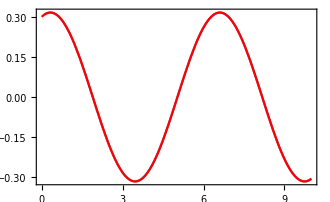

```mathematica
Show[
ListLinePlot[X1t],
Plot[ψ*.X1.ψ Cos[t] + ψ*.X2.ψ Sin[t],{t,0,nsteps Δt},PlotStyle->Red]
]
```